## 作用量

我们在经典力学中就开始接触作用量了，从经典力学里面的三种表述方法，到量子力学的三种表述方法，作用量现身的频率可谓不低。

那么什么是作用量？

### 经典力学

经典力学有三种表述方法，分别是 Euler-Lagrange 方程，Hamiltonian 正则方程以及 Hamiltonian-Jacobi 理论。这三种理论中，Euler-Lagrange 方程和 Hamiltonian-Jacobi 理论都需要用到作用量。那么作用量在经典力学中，是什么意思呢？

#### Action Principal

作用量原理是拉氏形式中最核心的内容。在这里，作用量是拉氏量在时间上的积分，

S=(∫_ti)^tf L(q(t),q'(t),t)dt=S(q(t))

也就是说，拉氏量是时间t，广义坐标q(t)，广义坐标对时间的导数q’(t) 的函数。但是作用量却只是广义坐标q(t)的函数。

我们先不管作用量原理，先看看这个作用量到底是什么意思。在一个保守力系中，拉氏量可以写成动能减去势能

L=T-V

那么作用量就是

S=(∫_ti)^tf(T-V)dt

这个很有趣。当我们选定一条路径之后，例如我们选定一个经典路径之后，作用量就是动能和势能对时间的曲线之间的面积。这样说起来太抽象，我们可以看一个自由落体运动的例子（从 x=0 开始沿 x 轴负方向下落）：

L=1/2 m x'^2-m g x

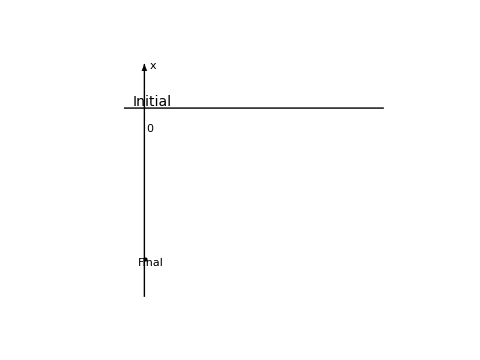

为了方便假定质量 m 为 1，那么如果我们选定经典轨道，那么就可以把动能和势能随着时间的变化关系画出来。

（经典轨道中，动能 T=(m g^2 t^2 )/2，势能 V=  - (m g^2 t^2) /2 ）

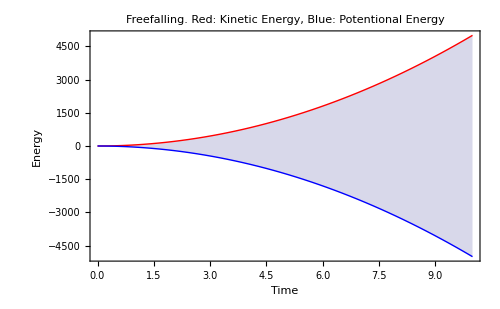

```mathematica
actEg1Plt1=Plot[{100 t^2/2,-100 t^2/2},{t,0,10},PlotLabel->"Freefalling. Red: Kinetic Energy, Blue: Potentional Energy",PlotStyle->{Red,Blue},FrameLabel->{"Time","Energy"},Filling->{1->{2}},Frame->True,ImageSize->500]
```

所以，对于这条经典路径，上面的阴影部分面积就是我们的路径积分的结果，即动能和势能的能量差值在整个时间上面的积分。

那么如果我们不是选取的经典路径呢？比如我们选取了这样一条路径：

x(t)=-g(t+1)^2

那么相应的，这条路径上的作用量就是对下面这个量在时间上的积分：

T-V = 2 g^2 (t+1)^2 - (- g^2 (t+1)^2)

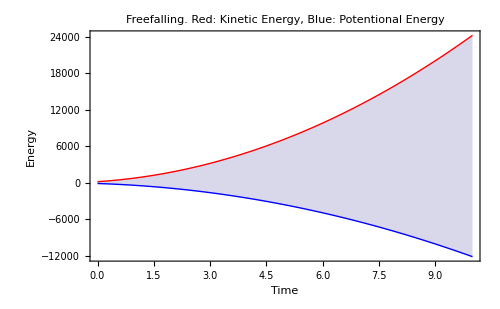

```mathematica
actEg1Plt2=Plot[{2 100 (t+1)^2,-100(t+1)^2},{t,0,10},PlotLabel->"Freefalling. Red: Kinetic Energy, Blue: Potentional Energy",PlotStyle->{Red,Blue},FrameLabel->{"Time","Energy"},Filling->{1->{2}},Frame->True,ImageSize->500]
```

作用量就是阴影区域的面积，看起来似乎是比原来大了，我们把两个图放在一起看看。

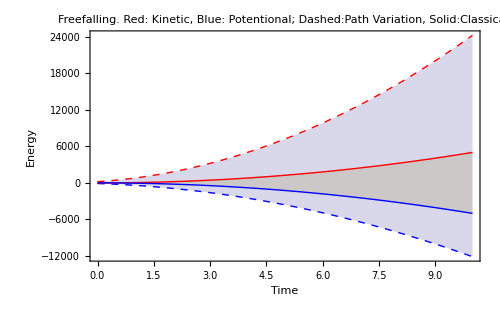

```mathematica
Plot[{Tooltip[2 100 (t+1)^2,"Kinetic Energy of New Path"],Tooltip[-100(t+1)^2,"Potential Energy of New Path"],Tooltip[100 t^2/2,"Kinetic Energy of Classical Path"],Tooltip[-100 t^2/2,"Potential Energy of Classical Path"]},{t,0,10},PlotRange->Full,PlotLabel->"Freefalling. Red: Kinetic, Blue: Potentional; Dashed:Path Variation, Solid:Classical;",PlotStyle->{Directive[Dashed,Red],Directive[Dashed,Blue],Red,Blue},FrameLabel->{"Time","Energy"},Filling->{1->{2},3->{4}},Frame->True,ImageSize->500]
```

从面积来看，选定的新路径下面作用量明显变大了。也就是说，在经典路径上面，作用量是最小的。
实际上大家可能注意到了，在作用量原理里面，我们所需要的基本假设少的可怜，我们连量纲、甚至能量守恒都可以不管不顾（上面的例子中，新路径的能量不守恒，可以自己画画看），只需要承认作用量原理，我们几乎获得所有的规则。这就是为什么作用量原理会显得更加基本。但是这也是很大的问题，从经典力学里面，我们似乎看不到为什么我们需要一个这样的原理，或者说，我们只知道这个原理起作用，但是并不是很明白为什么会有这个原理以及这个原理意味着什么。

从上面的保守力系的例子来看，最小作用量原理似乎要求整个过程中，动能和势能的相互转化要最小，否则会导致作用量变大。

/*不过我们不需要这么麻烦，在 Feymann Lectures 里面有一段讲这个的。我们模仿他。实际上我们可以把整个积分算出来。*/

我们可以再看看上抛运动的例子（初速度100[L]/[T]，实际路径：x=100t-1/2 g t^2, x’=100-g t；任选的路径：x=100t-1/2t, x’=100-t）：

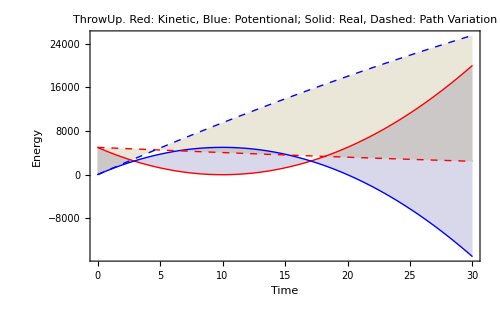

```mathematica
Plot[{1/2 (100-10t)^2,10(100t-5t^2),1/2 (100-t)^2,10(100t-1/2t^2)},{t,0,30},PlotLabel->"ThrowUp. Red: Kinetic, Blue: Potentional; Solid: Real, Dashed: Path Variation",PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"Time","Energy"},Filling->{1->{2},3->{4}},Frame->True,ImageSize->500]
```